# Spin of a Fidget Spinner

Measuring the rotation speed of a fidget spinner using sound.

Milad Pourrahmani (Miladiouss), Jun. 30,  2018

I was born in the early 1990s and I have witnessed the rise of the internet, smartphones, and social media. These inventions were surprising but not shocking. To me, it made sense why people would want to use the internet so they don’t have to go to a library, look at a screen while walking like zombies so they don’t have to deal with reality, or socialize online so they have to face each other face to face. But one thing that never made sense to me was the rise of fidget spinners. Just in case you don’t know what spinners are, let me enlighten you.

Sometime in the April of 2017, suddenly everyone owned these spinning toys that served no purpose. It just didn't make sense. Why did everyone owned a fidget spinner? To make the matter worse, these spinners were evolving. First, they were made of plastic and couldn't spin very long, then they acquired LED lights, and slowly, they became these luxurious toys made entirely of high quality metals with fancy auxiliary parts. As a full pledged hipster, I promised myself to avoid conformism and never buy one of these useless toys... (despite the temptation)!

Google Search Popularity of fidget spinners in early 2017:

```mathematica
sales=Import["https://upload.wikimedia.org/wikipedia/commons/thumb/7/76/Fidget_spinner_search_popularity_7d_rolling_mean.svg/585px-Fidget_spinner_search_popularity_7d_rolling_mean.svg.png"];
sales=ImageResize[sales,500]
```

-Graphics-

Though I didn't purchase one myself, soon I became a spinner owner when a friend of mine gave me a one as a Christmas gift. Little did they know what they have brought upon themselves! After playing with the spinner for a minute or two, it was soon clear what I had to do. I had to measure how fast my spinner was spinning and quantify its decay rate in middle of our holiday gathering.

```mathematica
christmasTree=Import["http://4.bp.blogspot.com/-EB2rrgiFNaU/Vm9IjjRw77I/AAAAAAAABgs/r7vSSyB_nig/s1600/christmas_PNG3769.png"];
ImageResize[christmasTree,300{1,1}]
```

-Graphics-

## Measurements

```mathematica
fidgitImageList=Import["https://i.stack.imgur.com/WnMrF.gif"]; (* I am miladiouss! *)
fidgitImageList=ImageResize[#,400{1,1}]&/@fidgitImageList;
ListAnimate[fidgitImageList,SaveDefinitions->True]
```

Since the spinners are too fast for phone cameras to fully capture their motion, I decided to make my measurements using sound. I looked around, I found a wooden coffee mixer. Then, I gave my spinner a good push and approached the mixer such that it would have minimal contact with the spinner and I recorded the resulting sound using SystemDialogInput["RecordSound"].

```mathematica
audio=-Graphics-;
```

The audio amplitude clearly peaks every time the spinner and the mixer touch. So let us attempt to extract the peaks from the audio.

## Data Curation

First, we extract useful information (i.e. audio duration and audio sampling rate) and convert the audio to a list of data points. Since we are aiming to extract the peak positions, we should take the absolute value of data points.

```mathematica
audioDuration = Duration[audio];
audioSampleRate = AudioSampleRate[audio];
data = First@AudioData[audio];
data = Abs @ data;
```

## Detect Peaks in Audio

Second, use PeakDetect to see which points are peaks (an output of 1) and which points are not peaks (an output of 0). Then find the location of peaks in seconds by dividing by audio sample rate. For display purposes, I am only plotting a small region of the data (after the clicking starts) and show the result of peak detect in that region. A total of 203 peaks were detected by our code.

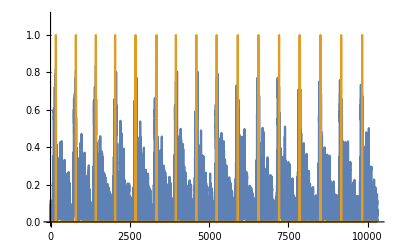

203

```mathematica
peaks = PeakDetect[data, 150, 0.0, 0.4];
peakPos = 1./audioSampleRate Position[peaks, 1]//Flatten;

ListLinePlot[
	{data⟦800 ;; 11111⟧, PeakDetect[data⟦800 ;; 11111⟧, 150, 0.0, 0.4]}, 
	PlotRange -> {All, {0, 1.1}}
]

Length[peakPos]
```

## Spin Rate

The period of the spinner is the separation between the peaks, times the number of blades. My unlike most common spinners, mine had six blades. We can achieve this by shifting peakPos and subtracting it from itself.

```mathematica
periods = 6 (peakPos⟦2 ;; -1⟧ - peakPos⟦1 ;; -2⟧);
```

Spin rate, that is revolutions per second, is reciprocal of the period:

```mathematica
spinRates = 1/periods;(*Revolutions per second*)
```

Convert the data into a list of {time, spin rate} and plot it:

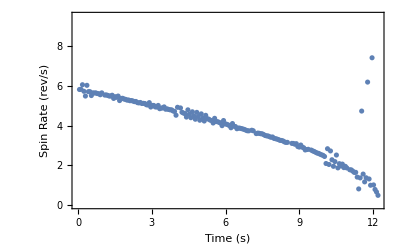

```mathematica
spinRateVStime = Table[{i audioDuration/Length[spinRates], spinRates⟦i⟧}, {i, Length[spinRates]}];

ListPlot[spinRateVStime, Frame -> True, FrameLabel -> {"Time (s)", "Spin Rate (rev/s)"}]
```

Let’s attempt to fit a data with a simple model.

```mathematica
model = spinCoef √(tEnd - t);
```

The misalignment of some points in the above plot are due to poor data collection (e.g. missed contacts between the blade and the mixer stick). This is also evident if we closely listen to the recorded audio. However, if we plot the entire range, we will see that there are other outliers that we can remove.

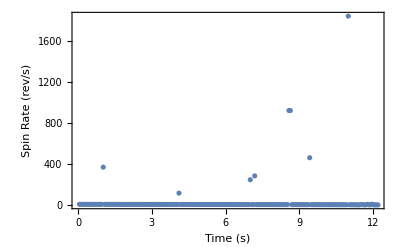

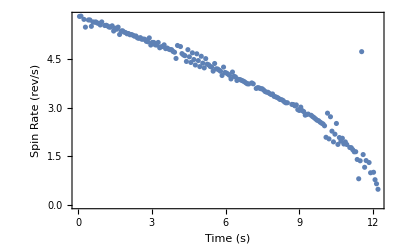

```mathematica
ListPlot[spinRateVStime, PlotRange -> All, Frame -> True, FrameLabel -> {"Time (s)", "Spin Rate (rev/s)"}]
(* Remove Units *)
fitData = Map[QuantityMagnitude, spinRateVStime, {2}];
(* Remove points with spin higher than 6 *)
fitData = DeleteCases[fitData, {_, s_}/; s > 6];
ListPlot[fitData, 
	PlotRange -> All, 
	Frame -> True, 
	FrameLabel -> {"Time (s)", "Spin Rate (rev/s)"}
]
```

Now we are ready to fit the data and plot it on top of our data.

{spinCoef→1.64801,tEnd→12.1433}

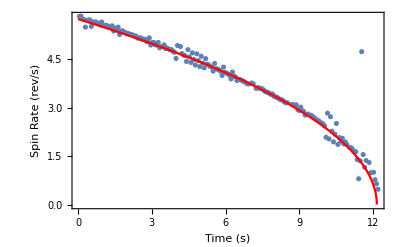

```mathematica
modelFit=FindFit[fitData,model,{{spinCoef,1.5},{tEnd,13}},t]//Quiet

Show[
	ListPlot[fitData, 
		Frame -> True, 
		FrameLabel -> {"Time (s)", "Spin Rate (rev/s)"}, 
		PlotRange -> All
	],
	Plot[model/.modelFit,{t, 0, 15}, PlotStyle -> Red, PlotRange -> All]
]
```

## Analysis of Results

We have address the objective of this essay, extracting the spin rate as a function . I tried to spin my spinner as fast as I could, which is about 6 revolutions per seconds. As a conclusion, I am quite sure that I will note receive any Christmas gifts from my friends anymore.

I will leave you with a unsolved puzzle.  Archeologist have discovered many of these mysterious objects called the Roman dodecahedrons and they do not know what function they served. I cannot stop to wonder what would future archeologist think when they find millions of fidget spinners. Or perhaps the Roman dodecahedron is nothing more than a ancient fidget spinner!

```mathematica
puzzle=Import["https://upload.wikimedia.org/wikipedia/commons/2/2d/Schwarzenacker_Pentagondodekaeder1.jpg"];
ImageResize[puzzle,400{1,1}]
```

-Graphics-

## Author contact information

mpourrah@uci.edu
Personal Email: miladiouss@gmail.com